# Test Rough Diffuse Beckmann

## License

/*
 * Copyright (c) <2023> NVIDIA CORPORATION & AFFILIATES. All rights reserved.
 *
 * Licensed under the Apache License, Version 2.0 (the “License”);
 * you may not use this file except in compliance with the License.
 * You may obtain a copy of the License at
 *
 *     http://www.apache.org/licenses/LICENSE-2.0
 *
 * Unless required by applicable law or agreed to in writing, software
 * distributed under the License is distributed on an “AS IS” BASIS,
 * WITHOUT WARRANTIES OR CONDITIONS OF ANY KIND, either express or implied.
 * See the License for the specific language governing permissions and
 * limitations under the License.
 */

## Compare eval() and sample()

```mathematica
Run["clang++ -I include test/rough_diffuse/test_rough_diffuse_beckmann_eval_sample.cpp -O3 -o test/rough_diffuse/test_rough_diffuse_beckmann_eval_sample"]
```

0

```mathematica
roughx="0.5";
roughy="0.1";
thetai="1.4";
kd=".7";
```

```mathematica
argstr=roughx<>" "<>roughy<>" "<>kd<>" "<>thetai<>" 1000000 100 > test/rough_diffuse/test_sample_eval.txt"
```

0.5 0.1 .7 1.4 1000000 100 > test/rough_diffuse/test_sample_eval.txt

```mathematica
Run["./test/rough_diffuse/test_rough_diffuse_beckmann_eval_sample "<>argstr]
```

256

```mathematica
check=Import["test/rough_diffuse/test_sample_eval.txt","Table"];
```

```mathematica
imEval=check[[-100;;-1]];
imSample=check[[2;;101]];
```

```mathematica
b=.5/Max[Flatten[imSample]];
gamma=0.3;
```

```mathematica
{Image[(b Abs[imEval])^gamma],Image[(b Abs[imSample])^gamma],(Image[(b Abs[imEval-imSample])^gamma])}
```

{-Graphics-,-Graphics-,-Graphics-}

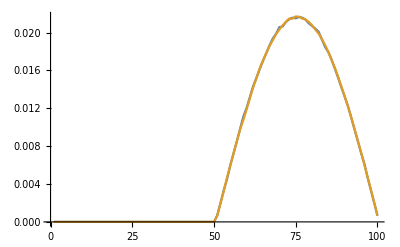

```mathematica
ListPlot[Total/@{Transpose[imSample],Transpose[imEval]},Joined->True]
```

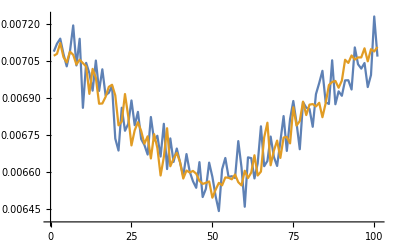

```mathematica
ListPlot[Total/@{imSample,imEval},Joined->True]
```